```mathematica
<<mf22.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
jNew[n_,m_]:=
Module[{ns,collect1,cf,collect2},
ns=Normal[J[n,m]]/.x->(2^6*m^3*x);
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];(* this division by cf might spoil interpolation *)
Return[collect2]]
```

```mathematica
leadingTermCoefficient[polynomial_]:=Module[{degree,leading},
degree=Exponent[polynomial,x];
leading=Coefficient[polynomial,x,degree];
Return[leading]]
```

```mathematica
rationalQ[x_]:=
IntegerQ[Numerator[x]]&&IntegerQ[Denominator[x]]&&!(Denominator[x]==0);
Attributes[rationalQ]=Listable
```

Listable

```mathematica
polyIsConstantQ[polynomial_]:=Module[{tf},
tf=False;
If[rationalQ[polynomial]==True,tf=True];
Return[tf]]
```

```mathematica
polyIsConstantQ[x]
```

False

```mathematica
polyIsConstantQ[3]
```

True

```mathematica
leadingTermCoefficient[11*x^2-x+1]
```

11

```mathematica
mckayThompson[n_]:=SeriesCoefficient[QPochhammer[-q,q^2]^24/q,{q,0,n}]
```

```mathematica
(* testing below code.... *)
fromPolyToNumberTimesMonic[polynomial_]:=
Module[{ltp},
ltp=leadingTermCoefficient[poly];
Return[{ltp,Collect[poly/ltp,x]}]]


baseConstantQ[pair_]:=
Module[{tf,bbase},
tf=False;
bbase=pair[[1]];
If[polyIsConstantQ[bbase]==True,tf=True];
Return[tf]
];
baseNotConstantQ[pair_]:=Not[baseConstantQ[pair]];

factorIntoMonics[polynomial_]:=
Module[{factor,factors,nonconstants,
lnf,lnt,lncf,monicfactor,monicfactorbase,monicfactors,numericalterm,k,kk,leadngterm,base,exponent,number,fpntm},
monicfactors={};
factors=FactorList[polynomial];

numericalterm=Select[factors,baseConstantQ];

lnt=Length[numericalterm];
number=Product[numericalterm[[kk,1]]^numericalterm[[kk,2]],{kk,1,lnt}];
nonconstants=Select[factors,baseNotConstantQ];
lncf=Length[nonconstants];
For[k=0,k<lncf,k++;
factor=nonconstants[[k]];
base=factor[[1]];
exponent=factor[[2]];
poly=base^exponent;
fpntm=fromPolyToNumberTimesMonic[poly];
number=number*fpntm[[1]];
AppendTo[monicfactors,fpntm[[2]]]];
Return[Flatten[{number,monicfactors}]]]

fromMonicFactorsToPolynomial[list_]:=
Module[{j,len,poly,base,exponent,pair},
poly=1;
len=Length[list];
For[j=0,j<len,j++;
poly=poly*list[[j]]];
Return[poly]]
```

```mathematica
stream=OpenWrite["run14sept20no1"];
For[m=2,m<302,m++;
jay=jNew[100,m];
Write[stream,{m,jay}]];
Close[stream]
```

run14sept20no1

```mathematica
stream=OpenRead["run14sept20no1"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

300

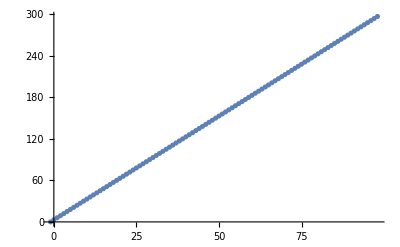

run14sept20no8

```mathematica
stream=OpenRead["run14sept20no1"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run14sept20no8"];
degrees={};
For[n=-2,n<98,n++;
data={};
For[k=0,k<300,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]];
ip=InterpolatingPolynomial[data,x];
ip=Expand[ip];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]];
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run14sept20no8"];
list=ReadList[stream];
Close[stream];
yes=0;
no=0;
yes2=0;
no2=0;
For[k=0,k<98,k++;
n=list[[k,1]];
poly=list[[k,2]];
If[PolynomialQ[poly,x]==True,yes++];
If[PolynomialQ[poly,x]==False,no++];
cl=CoefficientList[poly,x];
If[AllTrue[cl,rationalQ],yes2++];
If[Not[AllTrue[cl,rationalQ]],no2++]

];
Print[{yes,no,yes2,no2}]
```

{98,0,98,0}

```mathematica
stream=OpenRead["run14sept20no8"];
list=ReadList[stream];
Close[stream];
For[k=0,k<3,k++;
Print["======================================================================="];
n=list[[k,1]];
Print["n: ",n];
poly=list[[k,2]];
Print["monic-factor list: "];
fpoly=factorIntoMonics[poly];
Print[fpoly]]
```

=======================================================================

n: -1

monic-factor list:

{1}

=======================================================================

n: 0

monic-factor list:

{24,x,4/3+x^2}

=======================================================================

n: 1

monic-factor list:

{276,x^2,-16/23-(8 x^2)/69+x^4}